# Penning trap (analytical solution)

## Initial values and constants

```mathematica
ωE = 4.9;
ωB = 25.0;
ϵ = -1;
x0 = {10,0,0};
v0 = {50,0,20};
tEnd = 16;
```

## Equations of motion

In the z-direction

```mathematica
ωZ = Sqrt[-2ϵ]ωE;
z[t_] = x0[[3]] Cos[ωZ] + v0[[3]]/ωZ Sin[ωZ t];
```

In the x-y plane (w[t] = x[t] + i y[t])

```mathematica
SubMinus[Ω] = 1/2(ωB - Sqrt[ωB^2+4 ϵ ωE^2]);
SubPlus[Ω] = 1/2(ωB + Sqrt[ωB^2+4 ϵ ωE^2]);
SubMinus[R] = (SubPlus[Ω] x0[[1]] + v0[[2]])/(SubPlus[Ω]-SubMinus[Ω]);
SubPlus[R] = x0[[1]]-SubMinus[R];
SubMinus[T] = (SubPlus[Ω] x0[[2]] + v0[[1]])/(SubPlus[Ω]-SubMinus[Ω]);
SubPlus[T]  = x0[[2]] - SubMinus[T];
w[t_] = (SubPlus[R] + I SubPlus[T])Exp[-I SubPlus[Ω] t] + (SubMinus[R]+ I SubMinus[T]) Exp[-I SubMinus[Ω] t];
```

## Plotting the results

### x-y plane

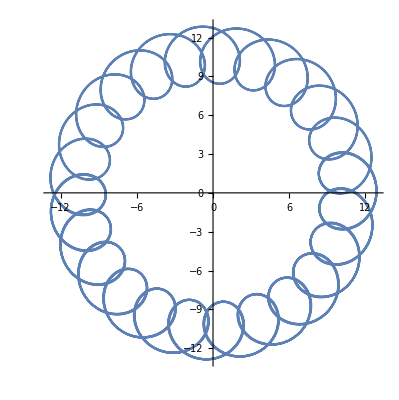

```mathematica
ParametricPlot[{Re[w[a]],Im[w[a]]}, {a, 0, tEnd}]
```

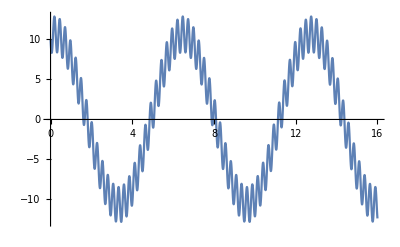

```mathematica
Plot[Re[w[a]], {a, 0, tEnd}]
```

### z-t plane

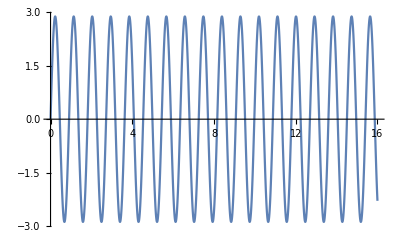

```mathematica
Plot[z[a], {a, 0, tEnd}]
```

### R-t

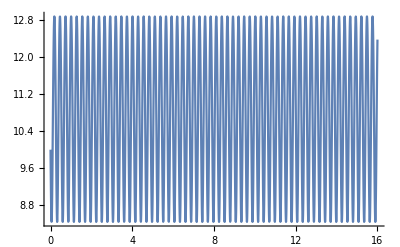

```mathematica
Plot[Abs[w[a]], {a, 0, tEnd}]
```

### 3D

```mathematica
ParametricPlot3D[{Re[w[a]], Im[w[a]], z[a]}, {a, 0, tEnd}]
```

-Graphics3D-